```mathematica
Exit[];
```

```mathematica
V=-Γ (Sin[Subscript[θ, 1][t]]+Sin[Subscript[θ, 2][t]]+Sin[Subscript[θ, 3][t]])+h1 Cos[Subscript[θ, 1][t]]+h2 Cos[Subscript[θ, 2][t]]+h3 Cos[Subscript[θ, 3][t]]+J(Cos[Subscript[θ, 1][t]]Cos[Subscript[θ, 2][t]]+Cos[Subscript[θ, 1][t]]Cos[Subscript[θ, 3][t]]+Cos[Subscript[θ, 2][t]]Cos[Subscript[θ, 3][t]])
```

h1 Cos[θ_1[t]]+h2 Cos[θ_2[t]]+h3 Cos[θ_3[t]]+J (Cos[θ_1[t]] Cos[θ_2[t]]+Cos[θ_1[t]] Cos[θ_3[t]]+Cos[θ_2[t]] Cos[θ_3[t]])-Γ (Sin[θ_1[t]]+Sin[θ_2[t]]+Sin[θ_3[t]])

```mathematica
eqs = Table[D[Subscript[θ, i][t], {t,2}] + D[V, Subscript[θ, i][t]]==0, {i, 1, 3}]/.{J->1,Γ->1, h1->1,h2->0,h3->0};
initValue = {Subscript[θ, 1][0]==π,Subscript[θ, 2][0]==π,Subscript[θ, 3][0]==0};
initDer = Table[Subscript[θ, i]'[0]==0,{i,1,3}];
(*initDer = {Subscript[θ, 1]'[0]==-2, Subscript[θ, 2]'[0]==-2,Subscript[θ, 3]'[0]==2};*)
{xsol,ysol,zsol} = NDSolveValue[Join[eqs, initValue, initDer], {Subscript[θ, 1], Subscript[θ, 2], Subscript[θ, 3]}, {t, 0, 10}];
Animate[ListPlot[{{Cos[xsol[t]] -Cos[ysol[t]]/2-Cos[zsol[t]]/2,Sqrt[3] Cos[ysol[t]]/2-Sqrt[3] Cos[zsol[t]]/2}}, PlotRange->{{-3, 3}, {-3,3}}], {t, 0, 10}]
```

```mathematica
sx = PauliMatrix[1];sz=PauliMatrix[3];id2=PauliMatrix[0];sy=PauliMatrix[2];
sx1 = KroneckerProduct[sx, id2, id2]; sx2 = KroneckerProduct[id2, sx, id2]; sx3 = KroneckerProduct[id2, id2, sx];
sz1 = KroneckerProduct[sz, id2, id2];sz2 = KroneckerProduct[id2, sz, id2];sz3 = KroneckerProduct[id2, id2, sz];
sy1 = KroneckerProduct[sy, id2, id2];sy2 = KroneckerProduct[id2, sy, id2];sy3 = KroneckerProduct[id2, id2, sy];
H =-Γ(sx1 + sx2 + sx3) + J(sz1.sz2+sz1.sz3+sz2.sz3) + h1 sz1 + h2 sz2 + h3 sz3;
```

## Define inputs

```mathematica
hParams = {J->1,Γ->1, h1->1,h2->0,h3->0};
initState = Flatten[KroneckerProduct[{0, 1}, {0, 1}, {1, 0}]];
initThetas = {Subscript[θ, 1][0]==π,Subscript[θ, 2][0]==π,Subscript[θ, 3][0]==0};
tf = 10;
dt = 0.1;
```

```mathematica
Clear[phit, psit, phi, psi]
```

```mathematica
phi[t_] = Table[Subscript[ϕ, i][t],{i, 1, 8}];
```

```mathematica
phiSol = NDSolveValue[{phi'[t]+ⅈ (H/.hParams).phi[t]==ConstantArray[0, 8], phi[0]==initState}, phi[t], {t, 0, tf}]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

```mathematica
getPsi[tf_, dt_]:=Module[{times, phit, ψop, ψt, rePsi, imPsi},
times = Table[tp, {tp, 0, tf, dt}];
phit = Table[phiSol/.{t->times[[i]]}, {i, 1, Length[times]}];
ψop = sz1 + sz2 Exp[2π ⅈ / 3]+sz3 Exp[4π  ⅈ / 3];
ψt = Table[ConjugateTranspose[phit[[i]]].ψop.phit[[i]], {i, 1, Length[phit]}];
{rePsi, imPsi} = {Re[#],Im[#]}&@ψt;

Return[{times, rePsi, imPsi}];
];
```

```mathematica
{times, rePsi, imPsi} = getPsi[tf, dt];
```

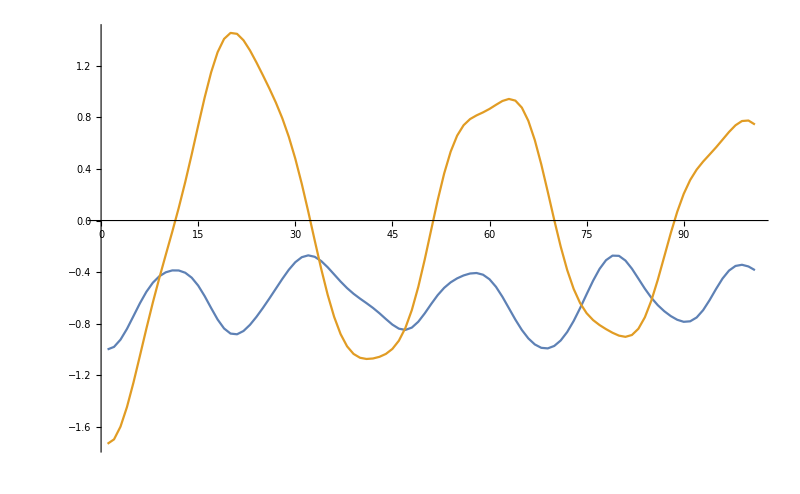

```mathematica
ListLinePlot[{rePsi, imPsi}]
```

```mathematica
moviePoints = Table[{rePsi[[i]], imPsi[[i]]}, {i, 1, Length[rePsi]}];
```

```mathematica
ListAnimate[Table[ListPlot[{moviePoints[[i]]}, PlotRange->{{-3,3},{-3,3}}], {i, 1, Length[moviePoints]}]]
```

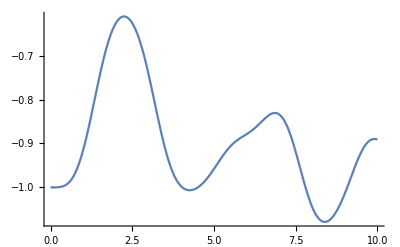

```mathematica
Plot[Cos[xsol[t]] -Cos[ysol[t]]/2-Cos[zsol[t]]/2, {t, 0, 10}]
```

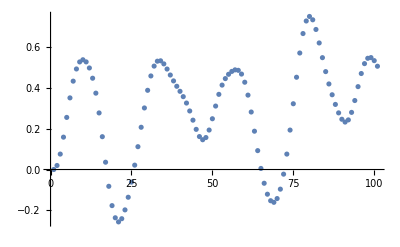

```mathematica
ListPlot[rePsi - Table[Cos[xsol[t]] -Cos[ysol[t]]/2-Cos[zsol[t]]/2, {t, times}]]
```

```mathematica
rePsi - Table[Cos[xsol[t]] -Cos[ysol[t]]/2-Cos[zsol[t]]/2, {t, times}]
```

{0.,0.0197226,0.0756389,0.158591,0.255281,0.351032,0.432979,0.492694,0.527186,0.537782,0.527388,0.497595,0.447363,0.374183,0.277249,0.160839,0.0357751,-0.0822404,-0.176942,-0.236484,-0.256682,-0.241038,-0.197814,-0.13591,-0.0617485,0.0214152,0.111887,0.207034,0.301637,0.388119,0.458464,0.506714,0.530759,0.532665,0.51765,0.492337,0.462996,0.434171,0.407834,0.383155,0.357057,0.325726,0.28685,0.241827,0.196774,0.161422,0.145908,0.156675,0.193418,0.248747,0.310904,0.368305,0.413636,0.445448,0.466602,0.480637,0.488271,0.486027,0.467709,0.427749,0.364514,0.281774,0.187756,0.0925297,0.00526702,-0.0673228,-0.120984,-0.152908,-0.160741,-0.142321,-0.0962277,-0.0227074,0.0755843,0.193258,0.322248,0.452138,0.57088,0.666196,0.727793,0.749969,0.733586,0.686248,0.620131,0.548097,0.479737,0.419268,0.366297,0.318952,0.277507,0.246279,0.232571,0.243106,0.279917,0.338003,0.406125,0.470391,0.518861,0.544977,0.54842,0.533467,0.506075}

```mathematica
ListPlot[imPsi - Table[Cos[xsol[t]] -Cos[ysol[t]]/2-Cos[zsol[t]]/2, {t, times}]]
```

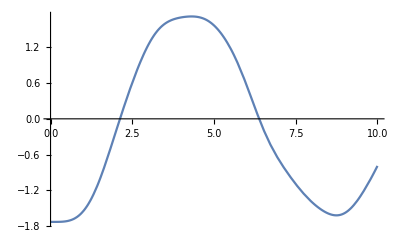

```mathematica
Plot[Sqrt[3] Cos[ysol[t]]/2-Sqrt[3] Cos[zsol[t]]/2, {t, 0, 10}]
```

```mathematica
quantAngles = ArcTan[imPsi / rePsi]
```

{1.0472,1.04717,1.04671,1.04452,1.0379,1.02184,0.987783,0.921653,0.799954,0.582671,0.219336,-0.25073,-0.63556,-0.858453,-0.970003,-1.01999,-1.03763,-1.0394,-1.03465,-1.02854,-1.02367,-1.02106,-1.021,-1.02362,-1.02919,-1.03759,-1.04707,-1.05206,-1.03937,-0.978341,-0.786865,-0.254223,0.50154,0.872372,1.0091,1.06093,1.07778,1.07793,1.06886,1.05356,1.0328,1.00625,0.973466,0.934482,0.889587,0.838143,0.776708,0.696564,0.580059,0.396226,0.108067,-0.267694,-0.610739,-0.839614,-0.972889,-1.04829,-1.0897,-1.108,-1.10656,-1.08659,-1.05068,-1.00287,-0.946081,-0.880052,-0.800936,-0.702089,-0.575611,-0.41523,-0.221167,-0.00470721,0.214148,0.41742,0.59757,0.756348,0.898662,1.02686,1.13729,1.2208,1.26763,1.27311,1.23939,1.17261,1.07822,0.957009,0.803642,0.61001,0.377236,0.130907,-0.0881064,-0.257224,-0.382494,-0.483796,-0.582098,-0.692832,-0.819501,-0.948739,-1.05678,-1.12598,-1.15246,-1.14035,-1.09389}

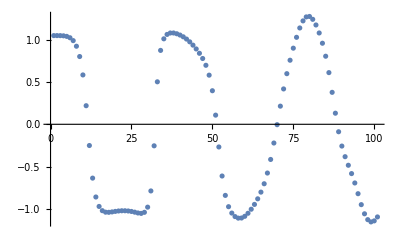

```mathematica
ListPlot[quantAngles]
```

```mathematica
classAngles = Table[ArcTan[(Sqrt[3] Cos[ysol[t]]/2-Sqrt[3] Cos[zsol[t]]/2)/(Cos[xsol[t]] -Cos[ysol[t]]/2-Cos[zsol[t]]/2)], {t, times}]
```

{1.0472,1.0472,1.0472,1.04719,1.04716,1.04706,1.04679,1.04616,1.0449,1.04255,1.03846,1.03169,1.02093,1.00436,0.979453,0.942649,0.888904,0.811031,0.699085,0.540963,0.327642,0.0669194,-0.205634,-0.445938,-0.632841,-0.769149,-0.866124,-0.934411,-0.981931,-1.01424,-1.03528,-1.04793,-1.05443,-1.05657,-1.05583,-1.05339,-1.05022,-1.04703,-1.04431,-1.04234,-1.0412,-1.04084,-1.04106,-1.04157,-1.04204,-1.04212,-1.04143,-1.03958,-1.03616,-1.03074,-1.02281,-1.01177,-0.996925,-0.977367,-0.951975,-0.91932,-0.877593,-0.824527,-0.757379,-0.673072,-0.568682,-0.44253,-0.295908,-0.134702,0.0307927,0.188915,0.330707,0.45194,0.55243,0.63422,0.700084,0.752726,0.794496,0.827381,0.853085,0.873115,0.888837,0.901479,0.912114,0.921628,0.930685,0.939713,0.948903,0.958237,0.967522,0.97644,0.984596,0.991561,0.996895,1.00016,1.0009,0.998664,0.992917,0.983066,0.96842,0.948172,0.921394,0.887035,0.843913,0.790731,0.726098}

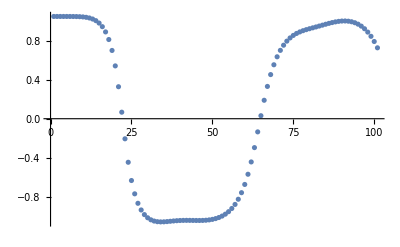

```mathematica
ListPlot[classAngles]
```

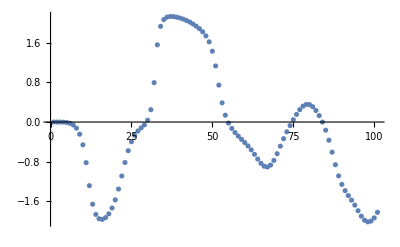

```mathematica
ListPlot[quantAngles-classAngles]
```